# Ejercicio 3

#### En cada uno de los siguientes incisos, grafica el campo de pendientes en la computadora y en la misma gráfica, añade las gráficas de algunas soluciones con distintas condiciones iniciales para verificar que concuerdan.

para

para

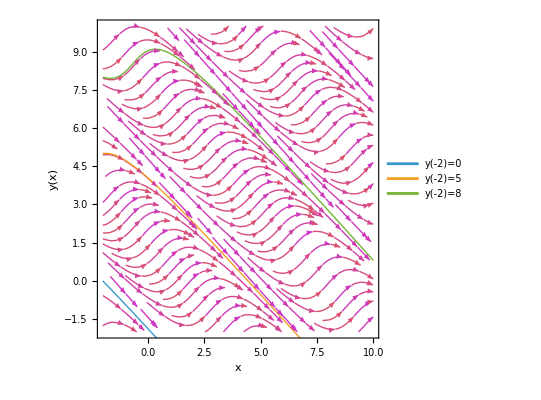

```mathematica
ClearAll["Global`*"]

(* 1) Definir la ecuación diferencial y la función f(x,y) *)
f[x_, y_] := Sin[x + y];

(* 2) Graficar el campo de pendientes con StreamPlot *)
slopeField = StreamPlot[
  {1, f[x, y]},
  {x, -2, 10},
  {y, -2, 10},
  Frame -> True,
  FrameLabel -> {"x", "y(x)"},
  PlotRange -> All,
  VectorScale -> None,
  StreamColorFunction -> Function[{x, y, u, v}, ColorData["NeonColors"][Norm[{u, v}]]],
  StreamColorFunctionScaling -> False
];

(* 3) Resolver numéricamente la EDO para distintas condiciones iniciales: y(-2)=0, 5 y 8 *)
soluciones = Table[
  NDSolve[
    {
      Derivative[1][y][x] == f[x, y[x]],
      y[-2] == y0
    },
    y,
    {x, -2, 10}
  ],
  {y0, {0, 5, 8}}
];

(* 4) Graficar todas las soluciones con etiquetas usando PlotLegends *)
solPlot = Plot[
  Evaluate[Table[y[x] /. soluciones[[i, 1]], {i, 1, Length[soluciones]}]],
  {x, -2, 10},
  PlotRange -> All,
  PlotStyle -> Thick,
  PlotLegends -> {"y(-2)=0", "y(-2)=5", "y(-2)=8"}
];

(* 5) Superponer el campo de pendientes y las soluciones *)
graficaFinal = Show[slopeField, solPlot];

graficaFinal
```

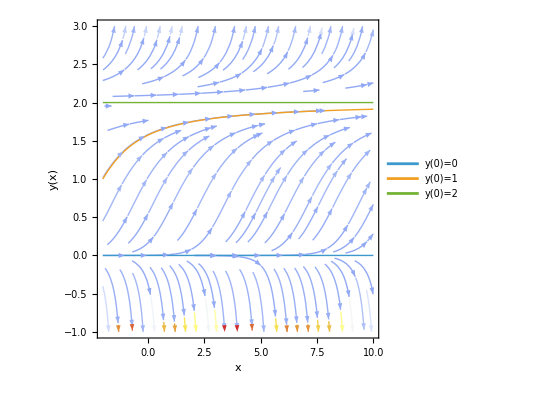

```mathematica
ClearAll["Global`*"]
(* 1)
   Ecuación diferencial: 
   y'[x] == (y[x]*(y[x]-2)^2)/2
*)
f[x_, y_] := (y(y-2)^2)/2;

(* --- 2) Campo de pendientes con StreamPlot --- *)
slopeField = StreamPlot[
  {1, f[x, y]},   (* Vector (dx/dt, dv/dt) "ficticio" => (1, dv/dx) en el plano (x,v) *)
  {x, -2, 10}, (* Rango para x, ajústalo según necesites *)
  {y, -1, 3},   (* Rango para v, en este caso sólo velocidades positivas *)
  Frame -> True,
  FrameLabel -> {"x", "y(x)"},
  PlotRange -> All,
  VectorScale -> None,
  StreamColorFunction -> Function[{x, y, u, v}, ColorData["TemperatureMap"][Norm[{u, v}]]],
  StreamColorFunctionScaling -> False
];

(* --- 3) Solución numérica con NDSolve --- *)
soluciones = Table[
  NDSolve[
    {
      Derivative[1][y][x] == f[x, y[x]],
      y[-2] == y0
    },
    y,
    {x, -2, 10}
  ],
  {y0, {0, 1, 2}}
];
(* 4) Graficar todas las soluciones sobre el mismo Plot *)
solPlot = Plot[
  Evaluate[Table[y[x] /. soluciones[[i,1]], {i, 1, Length[soluciones]}]],
  {x, -2, 10},
  PlotRange -> All,
  PlotStyle -> Thick,
  PlotLegends -> {"y(0)=0", "y(0)=1", "y(0)=2"}
];

(* 7) Superponer el campo de pendientes y las soluciones *)
Show[slopeField, solPlot]
```

# Ejercicio 6

Considere la ecuación diferencial

Grafica su campo de pendientes y basándote en él, determina el comportamiento cuando t → ∞. Encuentra la solución general y basándote en ella, confirma el comportamiento cuando t → ∞ que observaste antes.

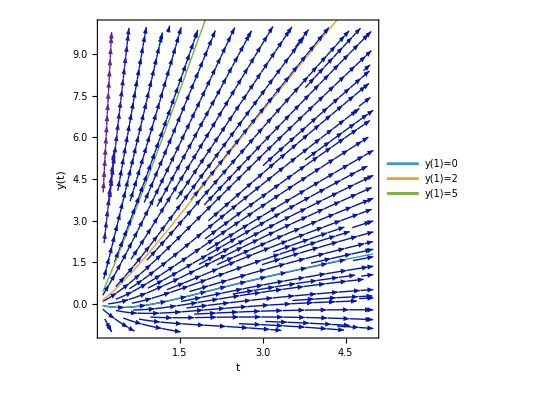

```mathematica
ClearAll["Global`*"]

(* Definir la función de la EDO en forma y' = f(t,y) *)
f[t_, y_] := (y + t^2 Exp[-t])/t  (*  =>  t*y' - y = t^2 e^-t *)

(* Graficar el campo de pendientes con StreamPlot.
   Interpretamos 't' en el eje horizontal y 'y' en el vertical. *)
slopeField = StreamPlot[
  {1, f[t, y]},
  {t, 0.1, 5},  (* evitamos t=0 para no dividir entre 0 *)
  {y, -1, 10},
  Frame -> True,
  FrameLabel -> {"t", "y(t)"},
  PlotRange -> All,
  VectorScale -> None,
  PlotTheme -> "Detailed"
];

(* Resolver la EDO numéricamente para distintas condiciones iniciales en t=1, por ejemplo *)
condIniciales = {y[1] == 0, y[1] == 2, y[1] == 5};
soluciones = Table[
  NDSolve[
    { t*y'[t] - y[t] == t^2 Exp[-t], cond },
    y, {t, 0.1, 5}
  ],
  {cond, condIniciales}
];

(* Graficar las soluciones y superponer con el campo de pendientes *)
solPlot = Plot[
  Evaluate@Table[y[t] /. soluciones[[i, 1]], {i, 1, Length[soluciones]}],
  {t, 0.1, 5},
  PlotRange -> All,
  PlotStyle -> Thick,
  PlotLegends -> {"y(1)=0", "y(1)=2", "y(1)=5"}
];

Show[slopeField, solPlot]
```